n = 400,   m = 800,   times = 5 * 10^4

```mathematica
simpleData[distro_]:=Module[{rv},
rv = {};
Do[
rv=Join[rv, Table[datum[[1]], {i, datum[[2]]}]];
,{datum, distro}
];
rv];
```

```mathematica
distro0=Import["/home/sam/Documents/School/rm/process_stats/degree_distro_R_400_800.dat", "FieldSeparators"->"\t"];
distroPlot =ListPlot[distro0, PlotMarkers->{Automatic,Medium}];
simple0 = simpleData[distro0];
mean = Mean[simple0];
ndPlot =DiscretePlot[Length[simple0]*PDF[PoissonDistribution[mean], x],{x,0,Length[distro0]}, PlotStyle->Purple, Joined->True];
Show[distroPlot, ndPlot]
PearsonChiSquareTest[simple0, PoissonDistribution[mean]]
```

#### I = 0.0

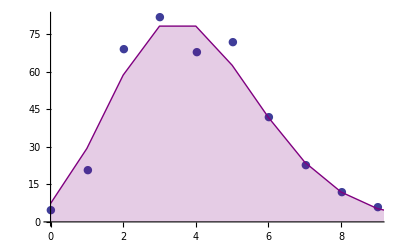

0.371567

```mathematica
distro1=Import["/home/sam/Documents/School/rm/process_stats/degree_distro_R_400_800_I1.dat", "FieldSeparators"->"\t"];
distroPlot =ListPlot[distro1[[2;;All]], PlotMarkers->{Automatic,Medium}];
simple1 = simpleData[distro1];
logLogData =DeleteCases[Table[If[datum[[2]]*datum[[1]]≠ 0,{Log[datum[[1]]],Log[datum[[2]]]}],{datum, distro1}], Null];

logLogFitEq =Fit[logLogData, {1, x}, x];
r = D[logLogFitEq, x];
powerFit =Fit[distro1[[2;;All]],{x^r},x];
powerPlot = Plot[powerFit, {x, 1, Length[distro1]}, PlotStyle->Purple];
Show[distroPlot, powerPlot, PlotRange->All]
PearsonChiSquareTest[distro1[[2;;All,2]], Table[powerFit,{x,1, Length[distro1]}]]
```

#### I = .99

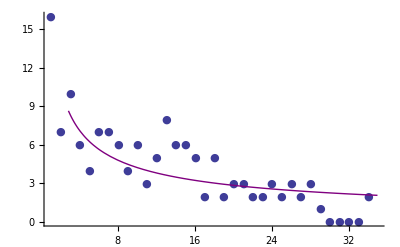

0.00998106